```mathematica
<<RQA`
```

Graphs and measurements taken from the Webber Chapter are highlighted in green.

## Henon

The version in the Webber paper seems to be off by 30± iterations... (but note that the data in the file doesn’t seem to match this).

```mathematica
α=1.4;β=0.3;nMax=2000;settle=30;
```

```mathematica
henonxy=
Drop[RecurrenceTable[{x[n+1]==1-α x[n]^2+y[n],
y[n+1]==β x[n],x[0]==0.0,y[0]==0.0},{x,y},{n,1,nMax+settle},DependentVariables->{x,y}],settle];
```

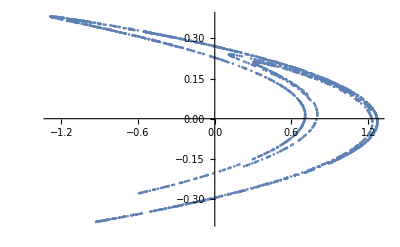

```mathematica
ListPlot[henonxy]
```

Convert into a time series

```mathematica
hts=TimeSeries[TemporalData[henonxy,{1,Automatic,1},ValueDimensions->2],ResamplingMethod->Automatic]
```

TimeSeries[…]

We’re dealing with a window 200-wide

```mathematica
tStart=1001;
w=200;
```

```mathematica
hw=TimeSeriesWindow[hts,{tStart,tStart+w-1}]
```

TimeSeries[…]

Make the 1D, x-only version

```mathematica
hx=TimeSeries[TemporalData[hw["Values"][[All,1]],{tStart,tStart+w-1,1}],ResamplingMethod->Automatic]
```

TimeSeries[…]

```mathematica
Export["~/Desktop/hcx",henonxy[[All,1]],"List"]
```

~/Desktop/hcx

The plot from Webber

and our data

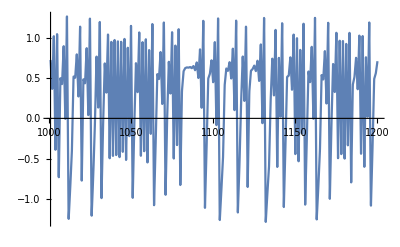

```mathematica
Plot[hx[t],{t,1001,1200}]
```

close... I had to shift the sequence by 30 cycles just to get the first ‘bursty’ section to align. There may be some more artifacts here and there. Notice the ‘bursty’ behavior around t=1050 in our data, but not in the Webber data. I tend to believe Mathematica’s numbers here. I have the data files from RQA141 and perhaps can re-create.

### Measures from my henon map

From the chapter:

Recurrence data computed from file HENCX using program RQD.EXE. RQA parameters: P1-Plast = 1001-1200; RANDSEQ = n; NORM = Euclid; DELAY = 1; EMBED = 3; RESCALE = max dist; RADUS = 3; COLORBND = 1; LINE = 2.

NB typo- I think he means ‘HENXC’ for the file name. Note that I’m not sure what RANDSEQ does here, as well as COLORBND. The RADIUS=3 doesn’t seem right, since points are (as you can see below) about a maximum of 3.0 units apart.

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

An unscaled distance map

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

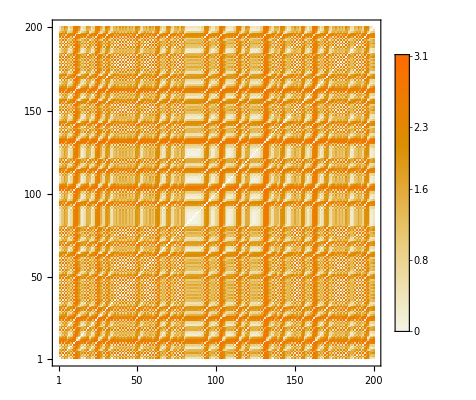

```mathematica
MatrixPlot[dm,DataReversed->True,PlotLegends->Automatic]
```

so, the RM claims that the ‘radius = 3’ but this really doesn’t make sense since that means that every point would be included... maybe it’s off by 100x?

Webber’s RM

Mine looks similar but definitely not the same. There seems to be some crazy spatial / sampling thing going on maybe (note the ‘bracket’ squiggles at (1150,1050) on Webber and around (50,50 which is actually 1050,1050) in mine)

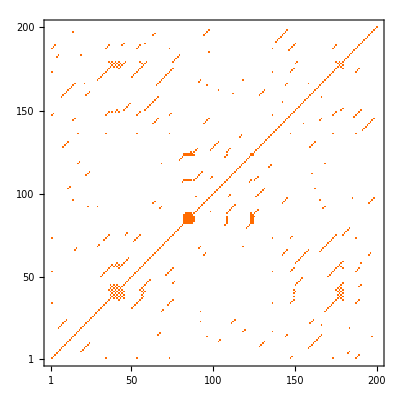

```mathematica
MatrixPlot[rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

From the chapter

%REC = 1.201; 
%DET = 88.703; 
LMAX = 12; 
ENT = 2.557; 
TND = –4.505; 
%LAM = 2.510; 
TT = 2.000.

#### Measures using my Henon calculations

Mine is not in % from personal preference. Off by .4% so I’m calling this a ‘match’.

```mathematica
RQARecurrence[rm]//N
```

0.0162312

Same with this

```mathematica
RQADeterminism[rm]//N
```

0.866873

Since LMAX is inversely proportional to the ‘chaos™’ in the system I’m returning it that way. Match.

```mathematica
RQAChaos[rm]//N
```

0.0833333

Entropy is close also.

```mathematica
RQAEntropy[rm]//N
```

2.62224

I think there’s a better way of calculating this w/o scaling the system up by 100,000 just to get a ‘pretty’ number. But- for the sake of what we have here, this is close.

```mathematica
RQATrend[rm]//N
```

-4.37773

I’m seeing a much greater laminarity here. 0.025 from the chapter...

```mathematica
RQALaminarity[rm]//N
```

0.111455

Similar with trapping time.

```mathematica
RQATrappingTime[rm]//N
```

4.5

In summary, everything is close-ish using the attractor I calculated. The laminarity is off, as well as the Trapping Time. Maybe this is due to my data?

### Measurements using Webber’s data file

I took the file HENXC from the RQA141 repository and turned it into the proper data structure.

```mathematica
whx=Import[NotebookDirectory[]<>"RQA141/HENXC","List"];
hx=TimeSeries[TemporalData[Take[whx,200],{tStart,tStart+w-1}],ResamplingMethod->Automatic]
```

TimeSeries[…]

From the chapter-

Alas, this data file doesn’t seem to be the above.

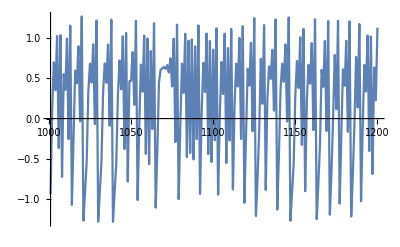

```mathematica
Plot[hx[x],{x,1001,1200}]
```

Scrolling through, I can’t find a place where it ‘visually’ matches.

```mathematica
Manipulate[ListLinePlot[Take[whx,{x,x+199}]],{{x,1},1,801}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[whx,{378.,577.}].

ListLinePlot::lpn: Take[whx,{378.,577.}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[whx,{378.,577.}].

ListLinePlot::lpn: Take[whx,{378.,577.}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[whx,{378.,577.}].

ListLinePlot::lpn: Take[whx,{378.,577.}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[whx,{378.,577.}].

ListLinePlot::lpn: Take[whx,{378.,577.}] is not a list of numbers or pairs of numbers.

This leads me to suspect the calculations?

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

A plot of the embedded function

```mathematica
ListPointPlot3D[Table[hxe3[t],{t,1001,1200,1}]]
```

-Graphics3D-

Note that the distance map is also different, the range of values is much greater, which is a little confusing.

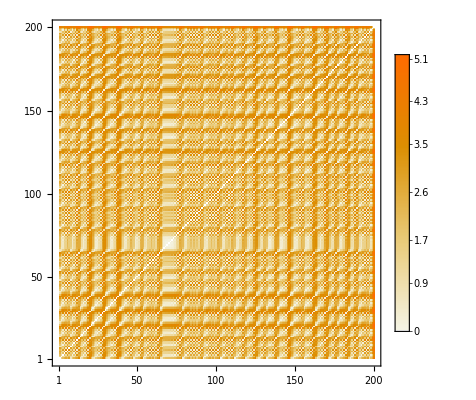

```mathematica
MatrixPlot[dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance],DataReversed->True,PlotLegends->Automatic]
```

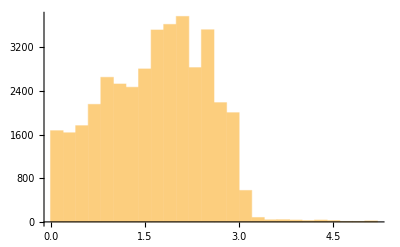

```mathematica
Histogram[Flatten[dm]]
```

Lots of weird, spurious values out past 3.

And, again, the RM looks ‘similar’ but not the same.

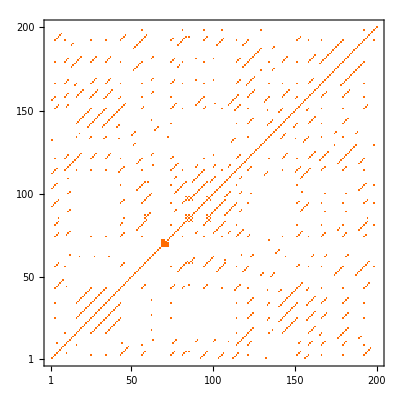

```mathematica
MatrixPlot[rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

#### Measures using HENXC

As a reminder

%REC = 1.201; 
%DET = 88.703; 
LMAX = 12; 
ENT = 2.557; 
TND = –4.505; 
%LAM = 2.510; 
TT = 2.000.

These measurements are also off, in some cases by a great amount, others, not so much

```mathematica
RQARecurrence[rm]//N
```

0.0286935

```mathematica
RQADeterminism[rm]//N
```

0.849387

```mathematica
RQAChaos[rm]//N
```

0.0526316

```mathematica
RQAEntropy[rm]//N
```

2.84694

```mathematica
RQATrend[rm]//N
```

-0.440203

```mathematica
RQALaminarity[rm]//N
```

0.0140105

```mathematica
RQATrappingTime[rm]//N
```

2.66667

So- the best I can tell, I can’t get the same results with the Webber data as are presented in the paper. I can get results that are close, but, even using the data supplied with the RQA141 package my results vary from those presented.

## EMG

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/flip/Dropbox/Research/RQA

```mathematica
emgC=Import["RQA141/EMGCONT","List"]
```

{-0.2,-0.21,-0.24,-0.26,-0.24,-0.25,-0.27,-0.27,-0.16,0.03,7980,-0.05,-0.07,-0.1,-0.12,-0.11,-0.08,0.,0.08,0.09,0.01}
 |  |  |  |

```mathematica
emgF=Import["RQA141/EMGFAT","List"]
```

{-0.26,-0.23,-0.21,-0.18,-0.09,0.11,0.57,1.13,1.53,1.54,1.37,7978,1.25,0.8,0.26,-0.13,-0.23,-0.04,0.21,0.39,0.33,0.13,-0.06}
 |  |  |  |

```mathematica
ts=RQAMakeTimeSeries[emgC,1/1000.]
```

TimeSeries[…]

The focus is on the first 1972 points of the time series digitized at 1000 Hz (displayed from 37 ms to 1828 ms).

```mathematica
tsw=TimeSeriesWindow[ts,{.037,1.828}]
```

TimeSeries[…]

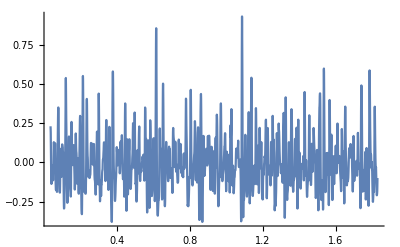

```mathematica
Plot[tsw[t],{t,tsw["FirstTime"],tsw["LastTime"]},PlotRange->All]
```

```mathematica
ee=RQAEmbed[tsw,10,0.004];
```

```mathematica
MatrixPlot[dm=RQADistanceMap[ee,DistanceFunction->EuclideanDistance],DataReversed->True,PlotLegends->Automatic]
```

-Graphics-

```mathematica
MinMax[dm]
```

{0.,5.5125}

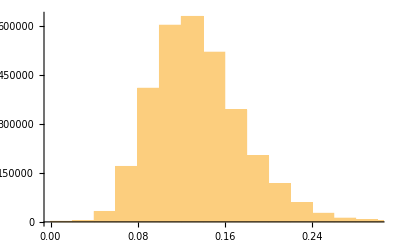

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

```mathematica
MatrixPlot[rm=RQARecurrenceMap[ee,0.05,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

-Graphics-

```mathematica
RQARecurrence[rm]*100.0
```

0.349092

```mathematica
RQADeterminism[rm]*100.0
```

63.1739

```mathematica
1.0/RQAChaos[rm]
```

118.

```mathematica
RQAEntropy[rm]//N
```

1.74805

```mathematica
RQATrend[rm]//N
```

-0.894049

```mathematica
RQATrappingTime[rm]//N
```

2.56404

```mathematica
ts["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
Mean[Differences[ts["Times"]]]
```

0.001

```mathematica
f=CorrelationFunction[ts,{1,100}]
```

CorrelationFunction::bdlag: The lag specification {0.1,0.1} should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

CorrelationFunction[TimeSeries[…],{0.1,0.1}]

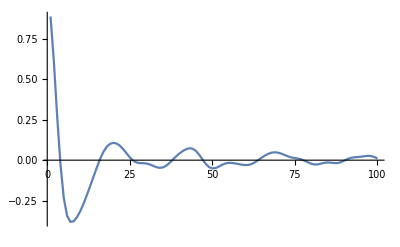

```mathematica
Plot[f[t],{t,1,100},PlotRange->All]
```

```mathematica
FindRoot[f[t],{t,1}]
```

{t→3.91575}

```mathematica
embedLag=RQAEstimateLag[ts]
```

0.00391575

```mathematica
RQAEstimateDimensionality[ts,embedLag]
```

{Null,{{{2,0.001375}}}}

```mathematica
e=RQATimeSeriesEpochs[tsw,1,0.25]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
e1=RQAEmbed[tsw,2,embedLag];
```

```mathematica
cNeighbors[ts_,OptionsPattern[]]:=Module[{nf},
	nf=Nearest[ts["Values"]];
	Position[ts["Values"],#]&/@ts["Values"]]
```

```mathematica
cNeighbors[tsw]
```

{{{1},{454},{487},{548},{809},{986},{1276},{1291},{1349},{1752}},1790,{{5},{14},{16},{61},{136},{207},{214},{215},{251},{301},37,{1523},{1548},{1556},{1602},{1612},{1632},{1715},{1730},{1740},{1792}}}
 |  |  |  |

```mathematica
d2=RQANeighborDistances[tsw,n]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0009,0.0009,0.0036,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0001,0.,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0036,0.0064,0.0009,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d1=RQANeighborDistances[e1,n]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.000367008,0.00179922,0.00421782,0.,0.000133972,0.014986,0.,0.0291872,0.,0.,0.,0.,0.,0.0038959,0.0417028,0.,0.,0.019131,0.00341353,0.0117321,0.,0.,0.,0.,0.0000439549,0.00194501,0.0104893,0.,0.113813,0.0869924,0.,0.,0.,0.,0.,0.00401578,0.0532883,0.000586254,0.00293902,0.300649,0.00501867,0.0495185,0.0357388,0.,0.0580051,0.00202997,0.148182,0.000309156,0.00887603,0.,0.,0.062922,0.0283299,0.0171198,0.0237816,0.0373493,0.000309156,0.036058,0.021009,0.,0.0658022,0.0433951,0.0591753,0.,0.00856136,0.,0.,0.,0.,0.00653552,0.00468203,0.202401,0.,0.150306,0.,0.,0.00717319,0.,0.136277,0.0062659,0.0413594,0.353959,0.00513875,0.,0.,0.0311981,0.,0.0090355,0.0728404,0.106137,0.,0.,0.0135768,0.,0.00931599,0.000703278,0.0981316,0.,0.0117082,0.320115,0.,0.00145115,0.110988,0.216958,0.147619,0.00401578,0.0616603,0.,0.,0.00194501,0.0370669,0.00840615,5.84265×10^-6,0.00964412,0.0269658,0.0765241,0.00750473,0.,0.0009,0.000178761,0.00160885,0.0342454,0.00258496,0.00181801,0.00105087,0.0788105,0.,0.0491443,0.0256354,0.0101692,0.0506499,0.0106854,0.00750473,0.00478275,0.055199,0.00380505,0.00933733,0.0158224,0.000850158,0.0060191,0.136196,0.000395594,0.544946,0.000664985,0.00117051,0.00885523,0.00401578,0.000069138,0.130128,0.3089,0.223282,0.140584,0.,0.0253311,0.,0.,0.0222479,0.34216,0.408381,0.25327,0.0317962,0.,0.00172845,0.,0.,0.631937,0.413925,0.,0.,0.00717319,0.,0.,0.,0.0184382,0.0884898,0.000305284,7.0987×10^-7,0.036058,0.0000838591,0.00140418,0.000156941,0.000156941,0.000223346,0.020555,2.47943×10^-6,0.0258348,0.146888,0.197976,0.227176,0.,0.,0.0124489,0.0060191,0.0124736,1.22005×10^-8,0.186352,0.0126625,0.00173765,7.0987×10^-7,0.177725,0.0370669,0.0333163,0.00501867,0.189177,0.0049,0.000951262,0.0009,0.000202001,0.00524424,0.056794,0.0465642,0.0380465,0.00624843,0.000117561,0.000754732,0.0106854,0.256674,0.00152467,0.0122616,0.195733,0.0769909,0.000470243,0.00358676,0.0120757,0.00964412,0.0225,0.0294758,1.73334×10^-31,0.000470243,0.00122114,0.0229749,0.0423484,0.0202826,0.0164647,0.0802986,0.0982009,0.00166811,0.115028,0.00311222,0.,0.00526025,0.00538318,0.0548039,0.23121,0.032744,0.00588907,0.0275221,0.0215327,0.0263435,0.0367008,0.00141247,0.0718152,0.345984,0.0400442,0.0993294,0.0212862,0.,0.,0.00166811,0.116098,0.00466693,0.000198873,0.0229749,0.0136025,0.00854093,0.0370244,0.09,0.0617152,0.00225363,0.00653552,0.00455252,0.0016,0.000801735,0.0309012,0.000249239,0.09,0.00241646,0.00340063,0.00240561,0.0175636,0.0291872,0.0920334,0.000627764,0.0154014,0.00341353,0.0121,0.000339495,0.00224315,0.000801735,0.0130445,0.0389953,0.0000879539,0.0662352,0.0196,0.1024,0.0719929,0.0275221,0.0103399,0.0025,0.018929,0.,2.47943×10^-6,0.0272432,0.00681081,0.000580918,0.0339343,0.0556478,0.22798,0.0126376,0.0662352,0.151358,0.132038,0.0126873,0.000115178,0.,7.0987×10^-7,0.0370244,0.00613323,0.036142,0.0126376,0.165944,0.0134067,0.436567,0.124198,0.0701957,0.0473423,0.0272432,0.,0.0400442,0.322025,0.326698,0.,0.,0.,0.0138257,0.0641964,0.0000574995,0.000502529,0.0272432,0.0136025,0.3219,0.0393288,0.0364209,0.165348,0.00600197,0.0225,0.0184682,0.0122861,0.00854093,0.000305284,0.00106524,0.0139984,0.125467,0.00274756,0.00209648,0.0154014,0.00122114,0.00950087,0.116174,0.000115178,0.0121,0.00488455,0.223975,0.00935869,0.00421782,0.0000439549,0.000664985,0.17358,0.0108603,0.00361327,0.0113699,0.0266177,0.0396197,0.0130445,0.26941,7.0987×10^-7,0.,0.00981031,0.04,0.0285769,0.0506002,0.028047,0.000470243,0.0128528,0.0173119,0.210053,0.0245675,0.000102221,0.0025,0.0342454,0.00478275,0.00856136,0.0235224,0.287972,0.00259621,0.0964858,0.266792,0.119645,0.368134,0.0441464,0.,0.00588907,0.,0.0198366,0.044408,7.0987×10^-7,0.000301437,0.000843729,0.,0.0339343,0.0434411,0.011191,0.0309012,0.0441,0.132731,0.0632898,0.0266898,0.0540691,0.00500303,0.0653707,0.0728404,0.0219973,6.38883×10^-6,0.0122616,0.00794905,0.0038959,0.0548556,0.264301,0.0821567,0.00209648,0.00432797,0.0113699,0.0215003,0.000305284,0.000117561,0.000305284,0.000156941,0.00117051,0.0389953,0.0160072,0.1764,0.0583583,0.0929913,0.0548556,0.0389953,0.0113699,0.0203141,0.0186677,0.0547005,0.0491443,0.0588732,0.015013,0.00856136,0.0458871,0.000033493,0.000102221,0.00735946,0.114953,0.0506002,0.0081,0.0517437,0.000117561,0.0320974,0.00563329,0.000276552,0.0193648,0.0532883,0.0935734,0.0220301,0.0039097,0.000395594,0.0179834,0.0701957,0.0719336,0.1089,0.0725052,0.0148342,0.0441,0.000202001,0.00233433,0.204019,0.17358,0.0248324,0.0342046,7.0987×10^-7,5.84265×10^-6,0.000470243,0.0580051,0.0000558366,0.0784,0.00146803,0.000202001,0.00550752,0.000893385,0.263436,0.0455268,0.00887603,0.0905062,0.0423939,0.127185,0.150135,0.00723439,0.00312456,0.0278023,0.0025,0.0450741,0.0440536,0.152758,0.129073,0.119645,0.000033493,0.,0.0855078,0.0734155,0.000715044,0.00792937,0.045121,0.0869924,0.0616603,0.000139135,0.00550752,0.,0.00341353,0.0376757,0.120152,0.0144,0.0584117,0.227874,0.000580918,0.0603571,0.108827,0.142485,0.00905651,0.0980624,0.120737,0.0765852,0.0548556,0.0158502,0.00105805,0.00233433,0.00412327,0.00512293,0.536435,0.0354625,0.107238,0.000470243,0.0240079,0.0215003,0.00653552,0.0465642,0.00146803,0.0242697,0.171481,0.00380505,0.0295137,0.0000454317,0.00869737,0.324066,0.0235224,0.021009,0.00653552,0.00380505,0.00423218,0.00232367,0.270285,0.520511,0.4621,0.829433,0.162707,0.316562,0.155065,0.0565478,0.163777,0.,0.0841,0.0831255,0.0506002,0.0498449,0.181919,0.399812,0.385171,0.145599,0.0317962,0.0232647,0.0559937,0.135036,0.172179,0.0544616,0.0101692,0.0021066,6.38883×10^-6,0.0198677,0.0277287,0.209281,6.38883×10^-6,0.000223346,0.000252739,1.22005×10^-8,0.0825769,0.033276,0.0166816,0.0062834,0.00171928,0.393583,0.379194,0.133881,0.158743,6.38883×10^-6,0.0557478,0.,0.,0.0106854,0.0119154,0.0357388,0.0502218,0.389504,0.00695058,0.0184682,0.000033493,0.00466693,0.0935734,2.83948×10^-6,0.053678,0.0716006,0.00110621,0.00111357,0.0001,0.00695058,0.0154014,0.00226413,0.000541013,0.0297658,0.000305284,0.0179834,0.198726,0.0175929,0.00293902,0.000754732,0.0225,0.0158502,0.00421782,0.0433491,0.0370244,0.00466693,0.0282927,0.0000168283,0.00141247,0.402086,0.180578,0.000434411,0.000507493,0.0004,0.147535,0.000586254,0.0224669,0.0399558,0.0454797,0.00952241,0.0129941,0.0294758,0.0177876,0.00600197,0.0253311,0.000115178,0.0230084,0.0845894,0.114532,0.00173765,0.00400179,0.00105805,0.00794905,0.18781,0.0576,0.0283671,0.290572,0.00638234,0.00901451,0.0188987,0.000439028,0.00179922,0.0588196,0.00400179,0.0203141,0.0000113579,0.0200434,0.0101692,0.224773,0.00501867,0.0128278,0.0487227,0.0864961,0.000546164,0.00811989,0.00794905,0.00379143,0.000136541,0.00808013,0.0182399,0.00794905,0.00241646,0.0472942,0.00767075,2.83948×10^-6,0.00340063,0.00792937,0.00274756,0.0245329,0.00167715,0.0001,0.000154186,0.0417028,0.000156941,0.00901451,0.0036,0.188445,0.0062659,0.151444,0.0028366,0.00613323,0.00538318,0.00159118,0.151444,0.0160351,0.00370181,0.0219973,0.000309156,0.015013,0.246641,0.0257993,0.222383,0.216174,0.154653,0.0175636,0.0855724,0.0409727,0.0361,0.055251,0.158655,0.0303116,0.136818,0.0286142,0.156648,0.0465642,0.0559937,0.00574372,0.00320694,0.0289,0.0169,0.00501867,0.0115503,0.000754732,0.00370181,0.0430448,0.00274756,0.0416126,0.179769,0.0164647,0.0120757,0.168882,0.0680965,0.0396637,0.0710915,0.0831892,0.0000168283,0.0117561,0.00122114,0.243305,0.00825237,0.0039097,0.00478275,0.0612426,0.000367008,0.0162774,0.000335436,0.0955783,0.00117051,0.0126625,0.0133811,0.142485,0.0755339,0.0215327,0.034558,0.0139984,0.00432797,0.00022666,0.00141247,0.253382,0.0113699,0.00202003,0.0779906,0.00681081,0.00110621,0.00796876,0.000720963,0.0479816,0.12839,0.0612426,0.045121,0.0875555,0.0240421,0.000434411,0.000664985,0.0960315,0.827899,0.496947,0.0437468,0.194245,0.,0.019231,0.11725,0.136918,0.307964,0.299726,0.339338,0.0156664,0.0108603,0.,0.155404,0.0472942,0.13815,0.12309,0.0733557,0.0387067,0.155894,0.0653707,0.0300189,0.0798219,0.0272432,0.0981316,0.00638234,0.0000439549,0.00840615,0.0105119,0.0025,0.157315,6.38883×10^-6,0.00172845,0.125986,0.00217434,0.00840615,0.0169,0.000580918,0.0158502,0.083612,0.00134175,0.00935869,0.00122114,0.0134067,0.0476614,0.015374,0.0487714,0.0420476,0.00917521,0.00152467,0.00950087,0.0250287,0.0294379,0.0110134,0.112262,0.0060191,0.0115741,0.00412327,0.210154,0.0137998,0.000070987,0.0596398,0.019131,0.0484,0.0179834,0.0345169,0.0136025,0.0103399,0.0203141,0.0604657,0.0184382,0.00166811,0.000843729,0.0128528,0.536435,0.0112143,0.0170909,0.0454797,0.00154197,0.0410174,0.00321946,0.0227202,0.00501867,0.276452,0.0427416,0.01,0.0038959,0.039285,0.00217434,0.101324,0.00268278,0.000627764,0.000156941,0.0690368,0.0929913,0.0850802,0.217061,0.0738128,0.00840615,0.229592,0.133265,0.00258496,0.0599979,0.0817375,0.389504,0.00550752,0.0444546,0.0144,0.00501867,0.0081,0.0277655,0.00794905,0.0351873,0.0000255553,0.0646241,0.0825769,0.000434411,0.184176,0.232726,0.134498,6.38883×10^-6,0.015013,0.0009,0.0434411,0.000154186,0.0339343,0.00825237,0.00160885,0.0351873,0.0386633,0.0348307,7.0987×10^-7,0.148182,0.00240561,0.0950581,0.00600197,0.00526025,0.00116296,0.0751926,0.0271704,0.0793465,0.0909473,0.0476614,0.141933,0.115028,0.00293902,0.00823231,0.0081,0.0632898,0.0454797,0.00154197,0.00312456,0.00141247,0.0261064,0.000670694,0.00723439,0.00134175,0.00141247,0.21383,0.01,0.00825237,0.000546164,0.0128528,0.00613323,0.0306057,0.0101692,0.0205233,0.0182698,0.0798843,0.142402,0.0235224,0.055251,0.0283299,0.0788105,0.161851,0.0389517,0.0117561,0.0258348,0.256674,0.0719336,0.179336,0.00752388,0.00340063,0.0506002,0.019131,0.1756,0.02801,0.044408,0.0188987,0.266037,0.00202003,0.0357805,0.0145762,0.0049,0.0016,7.0987×10^-7,0.0009,0.0009,0.0625,0.00128073,0.00721561,0.0136025,0.0333163,0.259987,0.00869737,0.00723439,0.0000347836,0.0367432,0.00442483,0.000580918,0.000622242,0.0264152,0.0200434,0.0355041,0.0191616,0.000305284,0.00432797,0.00412327,0.137524,0.0018086,0.00840615,0.0101692,0.00284837,0.00218466,0.00526025,0.00303108,0.015013,0.0412696,0.189911,0.116749,0.115675,0.181013,0.173488,1.21718,0.527088,0.312904,0.163777,0.00640284,0.155065,0.,0.104024,0.0556478,0.0576,0.,7.0987×10^-7,0.0286142,0.00241646,0.020555,0.0413594,0.011191,0.108272,0.0517437,0.0217807,0.00933733,0.0000454317,0.00709178,0.271392,0.020555,0.00721561,0.0250636,0.118987,0.156648,0.0490953,0.0098322,0.00950087,0.00209648,0.00370181,0.150703,0.105042,0.0632898,0.194245,0.0261064,0.000276552,0.0278023,0.000178761,0.0364209,0.00538318,0.0676574,0.000249239,0.00117051,0.00695058,0.000367008,0.162529,0.352826,0.34983,0.197325,0.0264152,0.0324398,0.000760813,0.00275915,0.0294758,0.0110134,0.0283299,0.00173765,0.0447638,0.056794,0.00501867,0.0354625,0.00478275,0.056794,0.0188987,0.000434411,0.00140418,0.00587213,0.00707319,0.000850158,0.0426959,0.00435709,0.0607718,0.259987,0.155317,0.0529,0.037392,0.000546164,0.0278023,0.0564456,0.0175636,0.0220301,0.000551339,0.00379143,0.0049,0.01,0.0517437,0.00682905,0.00501867,0.0314964,0.0587661,0.000309156,0.0231973,0.0339343,0.018013,0.207843,0.00935869,5.84265×10^-6,0.000754732,0.00241646,0.00779953,0.0162492,0.0105119,0.0333163,0.211498,0.000276552,0.0335436,0.0380035,0.0430906,0.0137998,0.179149,0.0062659,0.0039097,0.0141985,0.0315357,0.0118912,0.0386633,0.156648,0.00232367,0.118987,0.00792937,0.00466693,0.00117051,0.000465464,0.0495185,0.0600521,0.127787,0.175693,0.0825769,0.0495185,0.045121,0.00234502,0.174283,0.0476614,0.083612,0.045574,0.0714824,0.0986602,0.0358223,0.0502713,0.00840615,0.0203141,0.00128073,0.000136541,0.00550752,0.0160631,0.0000113579,0.0588196,0.1338,0.0637702,0.00513875,0.00808013,0.00524424,0.00217434,0.0009,0.139405,0.0769296,0.00301893,0.0596398,0.00361327,0.000709149,0.00349961,0.000475045,0.00821228,0.270285,0.0997216,0.100324,0.0245675,0.0529,0.0347895,0.00424657,0.0253311,0.00779953,0.0000858943,0.00105087,0.0320578,0.0889918,0.0743315,0.0437931,0.00241646,0.168009,0.0555957,0.00443954,0.0525131,0.000136541,0.00401578,0.0402934,0.11725,0.120152,0.0377186,0.045574,0.000622242,0.139405,0.0117321,0.0225,0.106137,0.0205233,0.0607718,0.0889918,0.0498449,0.0525131,0.015013,0.0667266,0.00576047,0.0286142,0.160088,0.000136541,0.0132123,0.021041,0.00434252,0.018013,0.0000558366,0.00105805,0.0529,0.00232367,0.0689207,0.00257374,0.000305284,0.0258703,0.00549114,0.0380465,0.0000818483,0.0419571,0.148182,0.174283,0.0624448,0.145683,0.0971476,0.028047,0.000280238,0.575042,0.252534,0.0253311,0.00106524,0.00027289,0.159239,0.19938,0.207843,0.0318356,0.0171487,0.00933733,0.0036,0.0138257,0.582565,0.00613323,0.00140418,0.0196,0.000136541,0.00456744,0.00919638,0.032704,0.00693218,0.0370244,0.00653552,0.0219973,0.017341,0.0821567,0.00153331,0.00750473,0.0433491,0.00179922,0.168009,0.0447638,0.0028366,0.00725319,0.0186074,0.0122616,0.019131,0.128994,0.165438,0.189911,0.00750473,0.00899355,0.3136,0.182107,0.0004,0.011191,0.282572,0.0250636,0.00122114,0.00421782,0.0198055,0.0025,0.0816744,0.0469285,0.0150401,0.00112095,0.0376757,0.0289,0.00153331,0.000951262,0.000664985,0.0036,0.00338776,0.00735946,0.194245,0.0599979,0.225677,0.0778672,0.00273599,0.0274854,0.340321,0.0817375,0.000659301,0.151358,0.132038,0.162707,0.0374347,0.0144,0.0729,0.00172845,0.00172845,0.228785,0.0108373,0.0711504,0.000133972,0.00284837,0.255821,0.0134067,0.00985412,0.0525638,0.0173119,0.0215003,0.0314964,0.021009,0.0000838591,0.0106854,0.00919638,0.000202001,0.000178761,0.00292705,0.00966582,0.000507493,0.000670694,0.000115178,0.00667245,0.217743,0.15022,0.0183782,0.0000673133,0.100789,0.246751,0.0283299,0.000664985,2.83948×10^-6,0.0049,0.00370181,0.0122861,0.00217434,0.000470243,6.38883×10^-6,0.0361,0.0170909,0.0510298,0.0250986,0.000546164,0.033276,0.00380505,0.0081,0.0025,0.0924782,0.00779953,0.0355041,0.00577725,0.00488455,0.0347895,0.00194501,0.0175343,0.000951262,0.00933733,0.0028366,0.0318356,0.00194501,0.00194501,0.00549114,0.0263793,0.217743,0.0000106256,0.0447638,0.0049,0.000223346,0.00101096,0.0143735,0.010147,0.0039097,0.139405,0.01,0.0845894,0.153991,0.0701957,0.0409727,0.137442,0.00811989,0.0128528,0.00341353,0.00919638,0.00233433,0.0224669,0.000249239,0.00133367,0.0214679,0.00292705,0.585141,0.0289,0.019131,6.38883×10^-6,0.0409727,0.0715415,0.0000439549,0.0039097,0.322856,0.00100394,0.0128528,0.238451,0.0145762,0.0802361,0.159327,0.00842642,0.0323602,0.00233433,0.219319,0.155317,0.131958,0.31442,0.0540177,0.109942,0.140035,0.18005,0.000198873,0.0126625,0.0992598,0.0576,0.341175,0.0064,0.0311981,0.00202997,0.0126625,0.0186979,0.0144265,0.0783382,0.00901451,0.169485,0.0090355,0.0205867,0.205244,0.172088,0.362025,0.193794,0.106759,0.00258496,0.,1.22005×10^-8,0.000249239,0.0207973,0.0250636,0.0258703,0.0203141,0.010147,0.000754732,0.000670694,0.0525131,0.135575,0.384263,0.0169,0.0997914,0.0256,0.0807141,0.0232647,0.11332,0.0198055,0.0367008,0.0266898,0.635786,0.0620794,0.0144265,0.0566888,0.27017,0.201742,0.304356,0.117903,0.00641769,0.,0.0036,0.0272797,0.00201012,0.0098322,0.0317962,0.0540691,0.0506002,0.00623098,0.00638234,0.00301893,0.0802361,0.0444546,0.000252739,0.0196,0.0532883,0.0756554,0.00217434,0.00122887,0.0196,0.00234502,0.239275,0.0025,0.17358,0.0137998,0.000069138,0.00225363,0.00964412,0.00284837,0.0396637,0.010147,0.0816744,0.00340063,0.00561672,0.00501867,0.0217481,0.000159721,0.0124489,0.0591216,0.075132,0.0458398,0.0625552,0.0476614,0.0106854,0.00443954,0.000627764,0.0139984,0.000754732,0.100254,0.00466693,0.00871799,0.0000255553,0.0215327,0.158655,0.174987,0.00935869,0.0000439549,0.0098322,0.0110366,0.0283299,0.0672199,0.0217155,0.0996519,0.034558,0.000115178,0.0062659,0.00351269,0.00536698,0.000801735,0.00468203,0.00225363,0.00707319,0.0122861,0.00885523,0.00370181,0.0182101,0.12952,0.00466693,0.0288625,0.0000425025,0.20392,0.361012,0.160675,0.0702543,0.0217807,0.00526025,0.00737843,0.0445012,0.00964412,0.0110366,0.00869737,0.0222809,0.0227535,0.0563931,0.0869924,0.00933733,0.0016,0.0469764,0.0427416,0.0393288,0.0253311,0.00811989,0.0134067,0.0224669,0.0367432,0.0158502,0.00917521,0.0156388,0.0154288,0.0122616,0.0641964,0.0855724,0.0761196,0.00105087,0.0326641,0.00122887,0.0440536,0.000580918,0.00194501,0.000367008,0.000760813,0.00513875,0.0245675,0.00750473,0.00842642,0.00854093,0.0563407,0.0177876,0.000580918,0.142569,0.00219499,0.00194501,0.245189,0.0000177468,0.0563931,0.0306057,0.000434411,0.000117561,0.00194501,7.0987×10^-7,0.00194501,0.00653552,0.01,0.0122861,0.00871799,5.84265×10^-6,0.00919638,0.379194,0.00968756,0.0997216,0.0229749,0.0611879,0.056046,0.0807141,0.00248897,0.105114,0.000136541,0.0184382,0.000507493,0.000664985,0.000580918,0.00179922,0.000280238,0.0563931,0.09,0.0373493,0.0506499,0.0249937,0.285147,0.26865,0.552599,0.277455,0.00538318,0.110015,0.0441,0.0556957,0.0117321,0.0291872,0.00100394,0.00370181,0.0637144,0.0162211,0.0737528,0.0402934,0.00304325,0.000202001,0.0555957,0.00792937,0.0306443,0.0616603,0.00128073,0.120152,0.0108373,0.000535887,0.615965,0.0286516,0.211702,0.00105087,0.00765142,0.0756554,0.00550752,0.00695058,0.015193,0.0000558366,0.000541013,0.00887603,0.0113935,0.0207655,0.356841,0.387403,0.0487714,0.000760813,0.0277287,0.0792221,0.443126,0.577432,0.269524,0.0320974,0.0477096,0.0393288,0.174987,0.0309012,0.0205233,0.00600197,0.00443954,0.000670694,0.000439028,0.000659301,0.345984,0.0041091,0.000154186,0.0145762,0.0351459,0.0517437,0.135036,0.00380505,0.000801735,0.000434411,0.00491548,0.000178761,0.000622242,0.0379604,0.145515,0.108345,0.225677,0.069422,0.0444546,0.00526025,0.255081,0.00966582,0.00808013,0.000154186,0.00512293,0.0294379,0.0108373,0.0220301,0.00166811,0.000033493,0.00188097,0.00134175,0.00105805,0.0860012,0.0693057}

```mathematica
neighborDistanceChange[d1_,d2_]:=MapThread[If[#1==0,0,Sqrt[(#2-#1)/#1]]&,{d1,d2}]
```

```mathematica
neighborDistanceChange[d1_,d2_]:=MapThread[Norm[{##}]&,{d1,d2}]
```

```mathematica
falseNeighborP[d1_,d2_,thresh_:10]:=Module[{d},
	d=neighborDistanceChange[d1,d2];
	N[Count[d,x_/;x>thresh]/Length[d2]]
]
```

```mathematica
d=neighborDistanceChange[d1,d2];
```

```mathematica
Count[d,x_/;x>.1]
```

293